# 1D First-Passage time. Want to check time scale and if the location of the boundary matters, likewise initial width

## Drift towards the equilibrium at (x, xh) = (0, 0) with an absorbing boundary at x*=1.

```mathematica
xf=30
tf=10
```

30

10

## Write down the Fokker-Planck equation

```mathematica
FP= D[p[x, t], t]== D[x*p[x, t], x] +D[p[x, t], {x, 2}]
```

p^(0,1)[x,t]==p[x,t]+x p^(1,0)[x,t]+p^(2,0)[x,t]

## Write down the boundary conditions

```mathematica
bcs ={p[xf, t]==0,
           p[1, t]==0
}
```

{p[30,t]==0,p[1,t]==0}

## And initial condition (distribution with the s.s. covariance, depends on parameters)

```mathematica
ip = Range[6, 16,2]
```

{6,8,10,12,14,16}

```mathematica
ic0 = Table[PDF[NormalDistribution[i, 2], x], {i, ip}]
```

{(ⅇ^(-1/8 (-6+x)^2))/(2 √(2 π)),(ⅇ^(-1/8 (-8+x)^2))/(2 √(2 π)),(ⅇ^(-1/8 (-10+x)^2))/(2 √(2 π)),(ⅇ^(-1/8 (-12+x)^2))/(2 √(2 π)),(ⅇ^(-1/8 (-14+x)^2))/(2 √(2 π)),(ⅇ^(-1/8 (-16+x)^2))/(2 √(2 π))}

```mathematica
n = Table[(p/.NDSolve[Join[{FP,p[x, 0]== i}, bcs],
                                   p,{x, 1,xf}, {t,0,tf}, Method->"MethodOfLines", MaxStepSize->0.05])[[1]], {i, ic0}]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

{InterpolatingFunction[{{1., 30.}, {0., 10.}}, <>],InterpolatingFunction[{{1., 30.}, {0., 10.}}, <>],InterpolatingFunction[{{1., 30.}, {0., 10.}}, <>],InterpolatingFunction[{{1., 30.}, {0., 10.}}, <>],InterpolatingFunction[{{1., 30.}, {0., 10.}}, <>],InterpolatingFunction[{{1., 30.}, {0., 10.}}, <>]}

```mathematica
Manipulate[Plot[n[[1]][x, t], {x, 1,xf}, PlotRange->{-0.01, 1}], {t, 0, tf}]
```

## Integrate to get survival probability

```mathematica
Surv = Table[Integrate[m[x, t], {x, 1, xf}],{m,n}]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

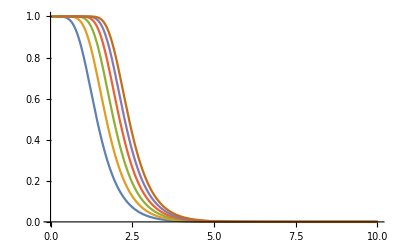

```mathematica
Plot[Surv,{t, 0, tf}, PlotRange->{0,1}]
```

## Get first-passage time probability

```mathematica
f = Table[-D[S, t], {S, Surv}]
```

{-InterpolatingFunction[…][t],-InterpolatingFunction[…][t],-InterpolatingFunction[…][t],-InterpolatingFunction[…][t],-InterpolatingFunction[…][t],-InterpolatingFunction[…][t]}

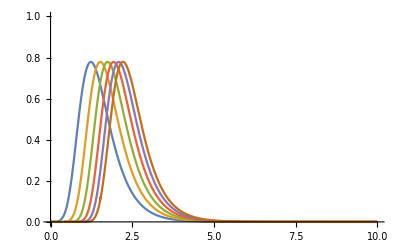

```mathematica
Plot[f,{t, 0, tf}, PlotRange->{0, 1} ]
```

```mathematica
norm = Table[NIntegrate[p, {t, 0, tf}], {p, f}]
mean = Table[NIntegrate[p*t, {t, 0, tf}], {p, f}]
second = Table[NIntegrate[p*t*t, {t, 0, tf}], {p, f}]
var = second - mean^2
```

{1.,1.,1.,1.,1.,1.}

{1.52372,1.81171,2.03586,2.21818,2.37233,2.50526}

{2.70446,3.665,4.5274,5.30298,6.0106,6.65888}

{0.382745,0.382703,0.382682,0.382666,0.382655,0.382568}

## Plots and scaling

## Behavior with v near crossover

```mathematica
x0Constant = 2
vCrossover = N[x0Constant*Erfc[x0Constant]]
vRange = Reverse[N[PowerRange[5*^-5,2*^-2 , 3]]]
 DConstant = 0.5
 kConstant = 1
```

2

0.00935547

{0.01215,0.00405,0.00135,0.00045,0.00015,0.00005}

0.5

1

```mathematica
results =FPT[DConstant,kConstant, x0Constant, #]&/@vRange
```

General::munfl: -5.07352×10^-307 (-0.0140515) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -5.07352×10^-307 0.0140515 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -5.07352×10^-307 (-0.00702576) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]}}

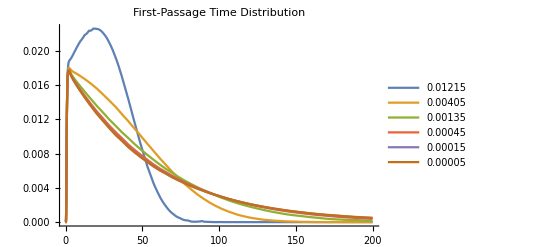

```mathematica
Plot[results, {t, 0, 200}, PlotRange->All, PlotLegends->vRange, PlotLabel->"First-Passage Time Distribution"]
```

## Behavior with x0 near crossover

```mathematica
x0Range = Range[1, 7, 1]
vConstant = 1*^-3
x0Crossover = FindRoot[vConstant - x*(1-Erf[x]), {x, 2}]
 DConstant = 0.5
kConstant = 1
```

{1,2,3,4,5,6,7}

1/1000

{x→2.50348}

0.5

1

```mathematica
results =FPT[DConstant,kConstant, #, vConstant]&/@x0Range
```

General::munfl: 3.29208×10^-306 (-0.00629723) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.93187×10^-308 (-0.00629723) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -4.08071×10^-308 (-0.00629723) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]}}

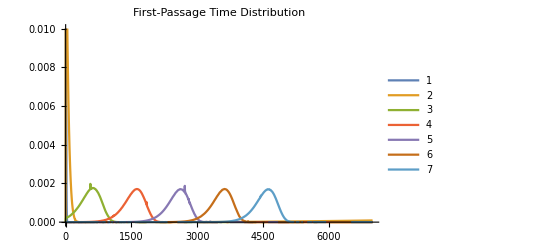

```mathematica
Plot[results, {t, 0, 7000}, PlotLegends->x0Range, PlotLabel->"First-Passage Time Distribution", PlotRange->{0, 0.01}]
```

#### Scaling with D

```mathematica
Clear[x0, d, v, k]
vConstant = 0.01
 DRange = PowerRange[0.1, 45, 2.7]
 kConstant = 1
x0Constant = 15
DCrossover = NSolve[(x0Constant/vConstant )== 1/Erfc[Sqrt[kConstant/(2*d)]*x0Constant], d]
```

0.01

{0.1,0.27,0.729,1.9683,5.31441,14.3489,38.742}

1

15

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{d→19.4301}}

```mathematica
results =FPT[#,kConstant, x0Constant, vConstant]&/@DRange
```

General::munfl: -9.57366×10^-308 (-0.00747168) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.57366×10^-308 0.00747168 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.57366×10^-308 (-0.00373584) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]},{-InterpolatingFunction[…][t]}}

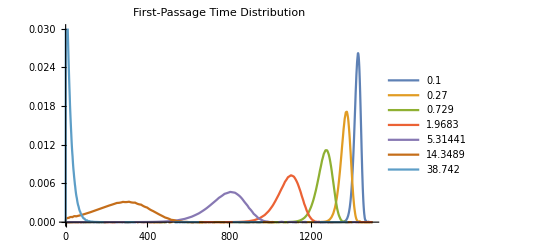

```mathematica
Plot[results, {t, 0, 1500}, PlotLegends->DRange, PlotLabel->"First-Passage Time Distribution", PlotRange->{0, 0.03}]
```